## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW250114";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_7"};
intermediateParams={};
mergerParams={};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1L_,chi2L_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,(*(* =====Alpha (并合段)=====*)"dalpha_3",IMRPhenomDAlphaNS[3,m1s,m2s,0,0],"dalpha_4",IMRPhenomDAlphaNS[4,m1s,m2s,0,0],"dalpha_2",IMRPhenomDAlphaNS[2,m1s,m2s,0,0],(* =====Beta (过渡段)=====*)"dbeta_2",IMRPhenomDBetaNS[2,m1s,m2s,0,0],"dbeta_3",IMRPhenomDBetaNS[3,m1s,m2s,0,0],*)(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)"dphi_0",IMRPhenomXASPhi[0,m1s,m2s,chi1L,chi2L],"dphi_2",IMRPhenomXASPhi[2,m1s,m2s,chi1L,chi2L],"dphi_3",IMRPhenomXASPhi[3,m1s,m2s,chi1L,chi2L],"dphi_4",IMRPhenomXASPhi[4,m1s,m2s,chi1L,chi2L],"dphi_5l",IMRPhenomXASPhiL[5,m1s,m2s,chi1L,chi2L],"dphi_6",IMRPhenomXASPhi[6,m1s,m2s,chi1L,chi2L],"dphi_6l",IMRPhenomXASPhiL[6,m1s,m2s,chi1L,chi2L],"dphi_7",IMRPhenomXASPhi[7,m1s,m2s,chi1L,chi2L],_,ConstantArray[0,Length[m1s]]]];


(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];],{p,allParams}];
```

```mathematica
samples["dphi_3"][[6]]
```

```mathematica
(*请自行修改 i 的范围：比如 1 到 Length[inspiralParams]*)Do[p=inspiralParams[[i]];
data=samples[p][[5]];
dist=EmpiricalDistribution[data];
percentile=100*CDF[dist,0.];
(*输出：i、p、对应的百分位数*)Print["i = ",i,"   |   p = ",p,"   |   百分位数 = ",percentile];,{i,1,Length[inspiralParams]}  (*自动遍历所有 i*)]
```

i = 1   |   p = dphi_2   |   百分位数 = 57.8547

i = 2   |   p = dphi_3   |   百分位数 = 40.1482

i = 3   |   p = dphi_4   |   百分位数 = 56.4208

i = 4   |   p = dphi_5l   |   百分位数 = 45.2346

i = 5   |   p = dphi_6   |   百分位数 = 66.9736

i = 6   |   p = dphi_7   |   百分位数 = 40.3643

```mathematica
|p-50|*2
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
```

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)
(*1. 数据提取与概率密度 (不变)*)
(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];m2Data=samples[p][[2]];
devData=samples[p][[5]];
grData=samples[p][[6]];   (*GR 系数值*)
paramData=samples[p][[7]];  (*GR*(1+d) 参数化值*)

m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

contourPD[p]={0.005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 147606 + 镜像 147606

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.005}，共 2 条

第一条前3点：{{31.8491,31.3457},{31.9344,31.2251},{31.9934,31.1826}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.971119

可信水平百分比：97.1119%

==========================

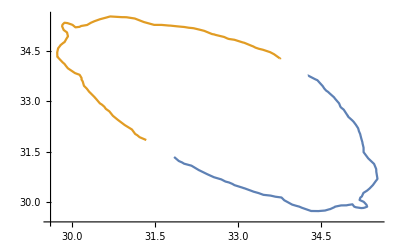

```mathematica
ListLinePlot[contourPoints[p]]
```

0.831126

0.5

dphi_2 grTargets = {6.22281,6.35214}

dphi_2 paramTargets = {5.83737,6.50536}

dphi_2 GR 线有效点数：下=8 上=13

dphi_2 参数化线有效点数：下=1 上=24

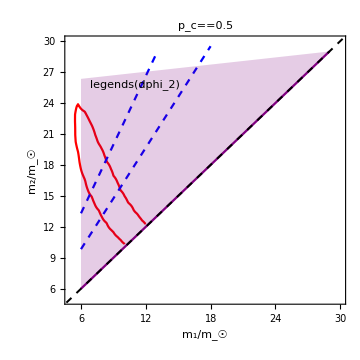

```mathematica
probability=prob
probability=0.5

(* ==========================================*)(*2. 解析参数名+计算目标值*)(* ==========================================*)
m1s=Range[5,30,1];m2s=Range[5,30,1];

pInterval=IntervalFromProbability[probability/2];

tapeIntervals["mass1"]=Quantile[m1Data,pInterval];
tapeIntervals["mass2"]=Quantile[m2Data,pInterval];

(*⭐ 解析参数名：自动拼出真实的物理函数*)
paramCore=StringDrop[p,1];  (*"dphi_2"->"phi_2"*)
{typeName,orderStr}=StringSplit[paramCore,"_"];
orderVal=If[StringEndsQ[orderStr,"l"],orderStr,ToExpression[orderStr]];
realFuncName=Symbol["IMRPhenomD"<>Capitalize[typeName]<>"NS"];

(*⭐⭐⭐ 关键修复：强制 N[] 确保目标值一定是数字 ⭐⭐⭐*)
grTargets=N[Quantile[N[grData],N[pInterval]]];     (*两个数字：{下界,上界}*)
paramTargets=N[Quantile[N[paramData],N[pInterval]]]; (*两个数字：{下界,上界}*)

(*打印验证*)
Print[p," grTargets = ",grTargets];
Print[p," paramTargets = ",paramTargets];


(* ==========================================*)
(*3. 反解（GR 和参数化用同一个公式，目标值不同）*)
(* ==========================================*)
(*物理含义：GR 线：IMRPhenomDPhiNS[2,m1,m2,0,0]==GR系数的分位数 参数化线：IMRPhenomDPhiNS[2,m1,m2,0,0]==参数化值的分位数 两者用的是同一个解析函数，区别只在目标值*)
theFormula=Function[{h,m2,c1,c2},realFuncName[orderVal,h,m2,c1,c2]];

chi1Fixed=0;chi2Fixed=0;
fixedArgs={chi1Fixed,chi2Fixed};
h0guess=N[Median[m1Data]];
h0s={h0guess,h0guess}; (*两个目标值需要两个初始猜测*)

Quiet[grSurface=HypersurfacePancake[theFormula,grTargets,{m2s},{1},fixedArgs,h0s,1];
paramSurface=HypersurfacePancake[theFormula,paramTargets,{m2s},{1},fixedArgs,h0s,1];];


(* ==========================================*)
(*4. 裁剪（GR 两条线+参数化两条线）*)
(* ==========================================*)
(*通用提取函数*)
extractLine[surface_,idx_]:=If[MatchQ[surface,{__List}]&&Length[surface]>=idx&&Length[surface[[idx]]]>1,Select[surface[[idx]][[2;;]],Function[pt,m2s[[1]]<=pt[[2]]<=m2s[[-1]]]],{}];

(*GR：下界线+上界线*)
grLineDown=extractLine[grSurface,1];
grLineUp=extractLine[grSurface,2];

(*参数化：下界线+上界线*)
lineDown=extractLine[paramSurface,1];
lineUp=extractLine[paramSurface,2];

Print[p," GR 线有效点数：下=",Length[grLineDown]," 上=",Length[grLineUp]];
Print[p," 参数化线有效点数：下=",Length[lineDown]," 上=",Length[lineUp]];


(* ==========================================*)(*6. 绘图（有啥画啥，哪怕只有一条边）*)(* ==========================================*)(*---动态组装线条---*)linesToPlot={};
plotStyles={};

(*红色：概率密度等值线（始终画）*)
AppendTo[linesToPlot,contourPoints[p][[1]]];
AppendTo[plotStyles,Red];

(*蓝色虚线：GR 反解线（有就画）*)
If[Length[grLineDown]>0,AppendTo[linesToPlot,grLineDown];
AppendTo[plotStyles,Directive[Blue,Dashed]]];
If[Length[grLineUp]>0,AppendTo[linesToPlot,grLineUp];
AppendTo[plotStyles,Directive[Blue,Dashed]]];

(*紫色：参数化反解线（有就画，哪怕只有一条边）*)
If[Length[lineDown]>0,AppendTo[linesToPlot,lineDown];
AppendTo[plotStyles,Purple]];
If[Length[lineUp]>0,AppendTo[linesToPlot,lineUp];
AppendTo[plotStyles,Purple]];


(*---Epilog 组装（彻底修复语法错误）---*)
epilogParts={};

(*1. 参数化区域填充（上下界都在时才填充，样式和图形基元平级）*)
If[Length[lineUp]>0&&Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Opacity[0.2]]];(*只有样式*)AppendTo[epilogParts,Polygon[Flatten[{lineUp,Reverse[lineDown]},1]]]; (*图形基元*)];

(*2. 画参数化边界线*)
If[Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineDown]];];
If[Length[lineUp]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineUp]];];

(*3. 图例和对角线（固定部分）*)
AppendTo[epilogParts,Directive[Black,Opacity[1]]];
AppendTo[epilogParts,Inset[legends[p],Scaled[{0.25,0.82}],{0,0}]];
AppendTo[epilogParts,Directive[Black,Dashed,Opacity[1]]];
AppendTo[epilogParts,Line[{{0,0},{100,100}}]];


(*---出图判断---*)
(*红色等值线+至少一条反解线 就画*)
If[Length[linesToPlot]>=2,ListLinePlot[linesToPlot,PlotStyle->plotStyles,Axes->False,Frame->True,FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->15},AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},Epilog->epilogParts,PlotLabel->With[{value=probability},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],ImageSize->Medium],(*一条反解线都没有时*)Print["提示：",p," 没有任何反解线，跳过绘图。"]]
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,45},{1,1.5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.20528};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p],PlotPoints->150,MaxRecursion->4];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]],1.5},"",False][[1]][[2]];
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];*)

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,45}

输入q范围：{1,1.5}

m1范围：{28.7175,63.5678}

m2范围：{23.5436,51.6914}

对称数据：原始 147606 + 镜像 147606

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.99999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

对称边界框：{23.5436, 63.5678} × {23.5436, 63.5678}

等高线值：{0.20528}，共 2 条

第一条前3点：{{32.6002,32.4755},{32.6012,32.4734},{32.6075,32.4583}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

警告：第 2 个区域点数不足，跳过积分

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.16

可信水平百分比：16.%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.16

```mathematica
m1m2PDF[p][34,34]
```

0.00422637

```mathematica
ListLinePlot[mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]]
```

Part::partw: Part 2 of {{{32.63,32.3879},{32.6325,32.3794},{32.6364,32.3666},{32.638,32.3601},{32.6408,32.3493},{32.6432,32.3409},{32.6445,32.3361},{32.6479,32.3216},{32.6492,32.3159},{32.6518,32.3049},«327»}} does not exist.

ListLinePlot::lpn: mergeSymmetricCurves[{{32.63,32.3879},{32.6325,32.3794},{32.6364,32.3666},{32.638,32.3601},{32.6408,32.3493},{32.6432,32.3409},{32.6445,32.3361},{32.6479,32.3216},{32.6492,32.3159},{32.6518,32.3049},«327»},{{{32.63,32.3879},{32.6325,32.3794},{32.6364,32.3666},{32.638,32.3601},{32.6408,32.3493},{32.6432,32.3409},{32.6445,32.3361},{32.6479,32.3216},{32.6492,32.3159},{32.6518,32.3049},«327»}}⟦2⟧] is not a list of numbers or pairs of numbers.

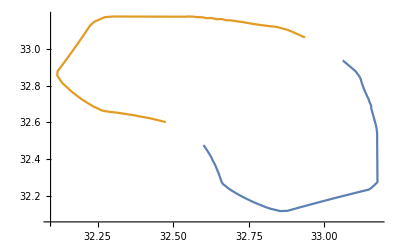

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

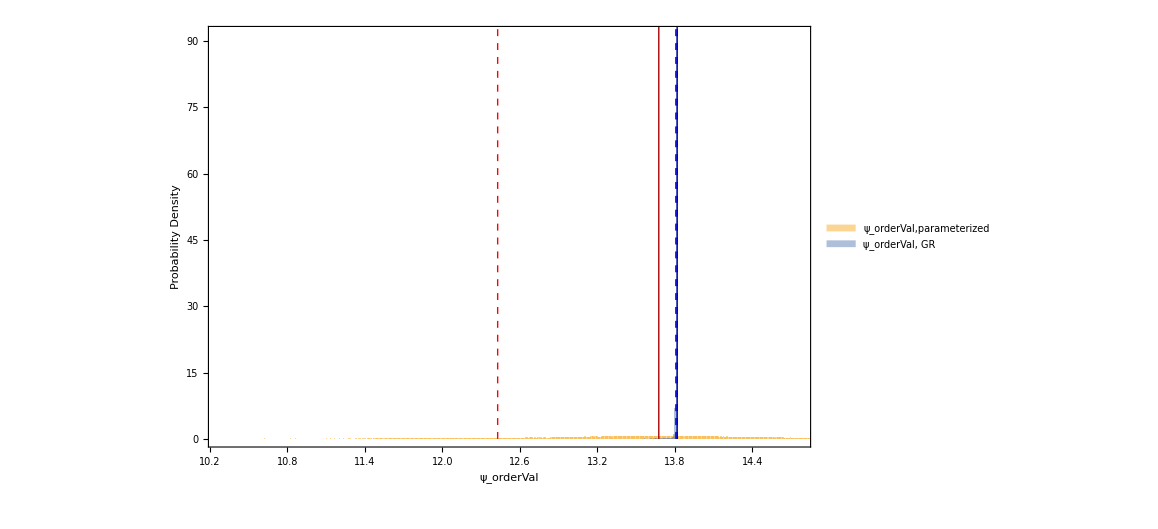

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.42, 0.58}

实际使用的 GR 概率区间上下界: {13.8167, 13.8173}

实际使用的 Param 概率区间上下界: {13.5303, 13.8172}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=8.59757×10^-16

GR上界: 点数=250 | Y>0点数=250 | 平均误差=8.95284×10^-16

Param下界: 点数=250 | Y>0点数=250 | 平均误差=5.54223×10^-16

Param上界: 点数=250 | Y>0点数=250 | 平均误差=8.45546×10^-16

chi1L取值：-0.0486105

chi2L取值：-0.0272827

=====================================================

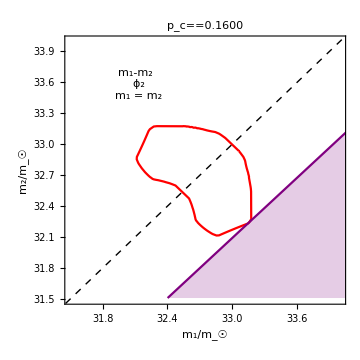

```mathematica
probability=prob;
(*probability=0.16;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,45},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.16533};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p],PlotPoints->150,MaxRecursion->4];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,45}

输入q范围：{1,2}

m1范围：{28.7175,73.9688}

m2范围：{20.5469,51.6914}

对称数据：原始 148303 + 镜像 148303

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

对称边界框：{20.5469, 73.9688} × {20.5469, 73.9688}

等高线值：{0.16533}，共 2 条

第一条前3点：{{32.2836,32.4505},{32.2676,32.4654},{32.2442,32.4857}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.292956

可信水平百分比：29.2956%

==========================

dphi_3 预处理完成，红线包含概率 prob = 0.292956

```mathematica
m1m2PDF[p][34,34]
```

0.00422637

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

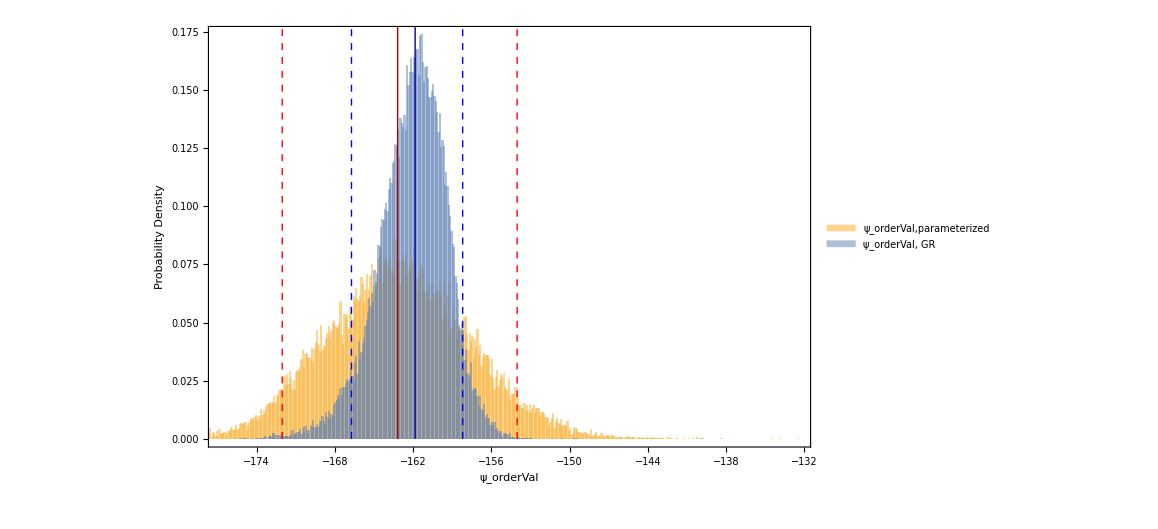

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.353522, 0.646478}

实际使用的 GR 概率区间上下界: {-162.805, -160.945}

实际使用的 Param 概率区间上下界: {-165.166, -161.159}

GR下界: 点数=175 | Y>0点数=175 | 平均误差=0.

GR上界: 点数=175 | Y>0点数=162 | 平均误差=0.175834

Param下界: 点数=175 | Y>0点数=175 | 平均误差=2.19977

Param上界: 点数=175 | Y>0点数=175 | 平均误差=0.

chi1L取值：-0.0426986

chi2L取值：-0.0227578

=====================================================

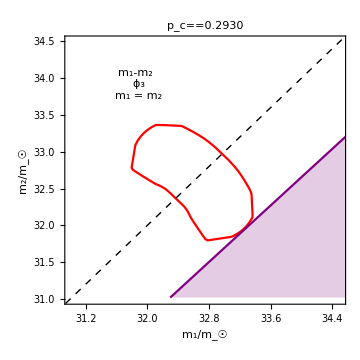

```mathematica
probability=prob;
(*probability=0.28;*)

plots[p]=PlotInversion[p,probability,31,34.5,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.17228};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p],PlotPoints->150,MaxRecursion->4];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 145184 + 镜像 145184

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.17228}，共 2 条

第一条前3点：{{32.6701,32.5545},{32.6752,32.5509},{32.6848,32.5482}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.135034

可信水平百分比：13.5034%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.135034

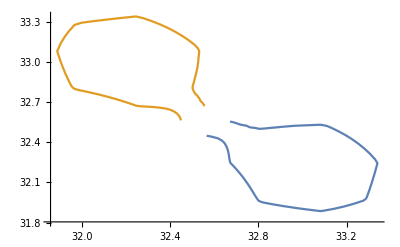

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

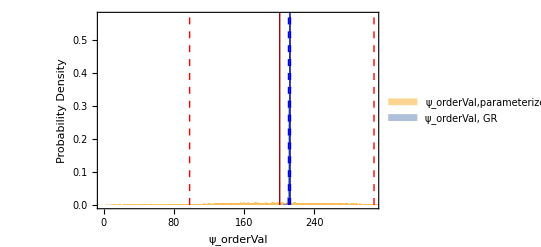

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
m1m2PDF[p][33,32.5]
```

0.17571

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.432483, 0.567517}

实际使用的 GR 概率区间上下界: {212.007, 212.206}

实际使用的 Param 概率区间上下界: {189.027, 212.436}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=1.96678×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=1.28466×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=2.12594×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=1.58025×10^-14

chi1L取值：-0.0439774

chi2L取值：-0.0295357

=====================================================

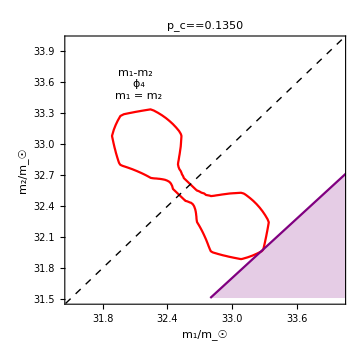

```mathematica
probability=prob;
(*probability=0.135;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0575};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 143483 + 镜像 143483

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.0575}，共 2 条

第一条前3点：{{33.5772,33.4619},{33.5775,33.4619},{33.5812,33.458}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.715313

可信水平百分比：71.5313%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.715313

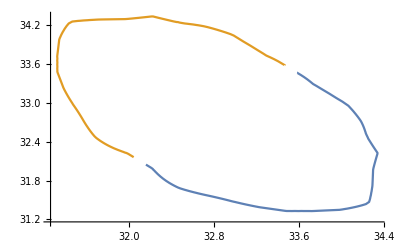

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

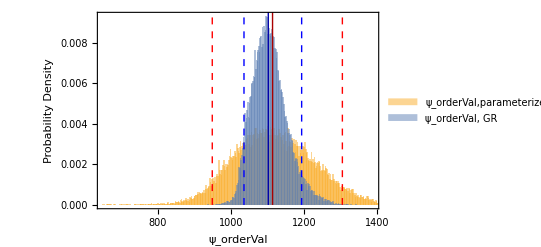

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.142344, 0.857656}

实际使用的 GR 概率区间上下界: {1056.4, 1157.16}

实际使用的 Param 概率区间上下界: {1002.16, 1240.4}

GR下界: 点数=450 | Y>0点数=450 | 平均误差=22.8509

GR上界: 点数=450 | Y>0点数=450 | 平均误差=32.6515

Param下界: 点数=450 | Y>0点数=450 | 平均误差=77.0881

Param上界: 点数=450 | Y>0点数=450 | 平均误差=115.887

chi1L取值：-0.019432

chi2L取值：-0.0232529

=====================================================

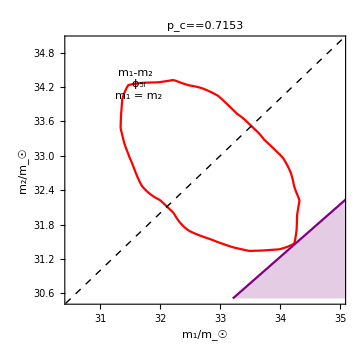

```mathematica
probability=prob;
(*probability=0.7;*)
plots[p]=PlotInversion[p,probability,30.5,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiL,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

0.175

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4125, 0.5875}

实际使用的 GR 概率区间上下界: {1092.84, 1112.93}

实际使用的 Param 概率区间上下界: {1090.04, 1140.17}

GR下界: 点数=450 | Y>0点数=450 | 平均误差=2.03626×10^-13

GR上界: 点数=450 | Y>0点数=450 | 平均误差=2.27374×10^-13

Param下界: 点数=450 | Y>0点数=450 | 平均误差=4.50705×10^-13

Param上界: 点数=450 | Y>0点数=450 | 平均误差=2.89522×10^-13

chi1L取值：-0.0316921

chi2L取值：-0.0232529

=====================================================

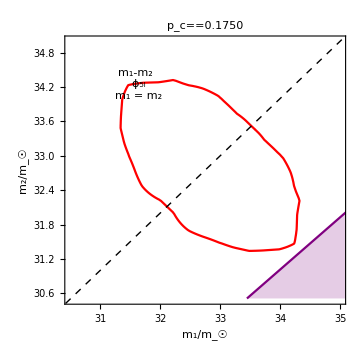

```mathematica
probability=0.175
plots[p]=PlotInversion[p,probability,30.5,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiL,spinPercentile1->0.45,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.15141};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 135767 + 镜像 135767

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.15141}，共 2 条

第一条前3点：{{32.5632,32.4478},{32.5634,32.4479},{32.5831,32.4016}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.255635

可信水平百分比：25.5635%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.255635

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

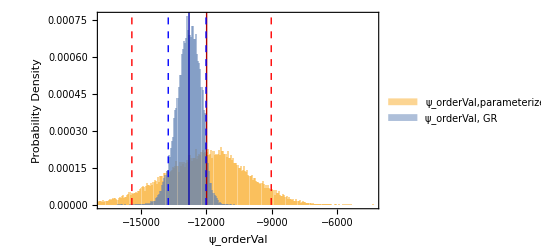

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.372182, 0.627818}

实际使用的 GR 概率区间上下界: {-12977.7, -12614.5}

实际使用的 Param 概率区间上下界: {-12617.5, -11377.2}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=358.112

GR上界: 点数=250 | Y>0点数=250 | 平均误差=4.09636×10^-12

Param下界: 点数=250 | Y>0点数=250 | 平均误差=3.33966×10^-12

Param上界: 点数=250 | Y>0点数=250 | 平均误差=2.38651×10^-12

chi1L取值：-0.032519

chi2L取值：-0.0183631

=====================================================

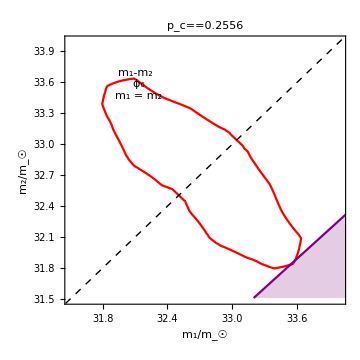

```mathematica
probability=prob;
(*probability=0.255;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,1.5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
(*q<=2*)
(*contourPD[p]={0.16305384};*)
(*contourPD[p]={0.1629871};*)
contourPD[p]={0.162987};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,1.5}

m1范围：{28.7175,49.4416}

m2范围：{23.5436,40.2044}

对称数据：原始 143218 + 镜像 143218

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{23.5436, 49.4416} × {23.5436, 49.4416}

等高线值：{0.162987}，共 2 条

第一条前3点：{{32.6186,32.6966},{32.6132,32.6992},{32.6047,32.7031}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.254659

可信水平百分比：25.4659%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.254659

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

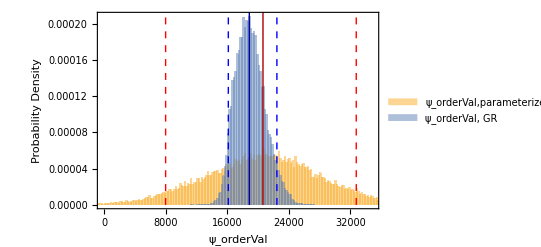

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.37267, 0.62733}

实际使用的 GR 概率区间上下界: {18234.1, 19514.6}

实际使用的 Param 概率区间上下界: {18230.9, 22969.5}

GR下界: 点数=400 | Y>0点数=400 | 平均误差=1.92813×10^-12

GR上界: 点数=400 | Y>0点数=400 | 平均误差=1216.29

Param下界: 点数=400 | Y>0点数=400 | 平均误差=1.71894×10^-12

Param上界: 点数=400 | Y>0点数=400 | 平均误差=4671.28

chi1L取值：-0.0325528

chi2L取值：-0.0219549

=====================================================

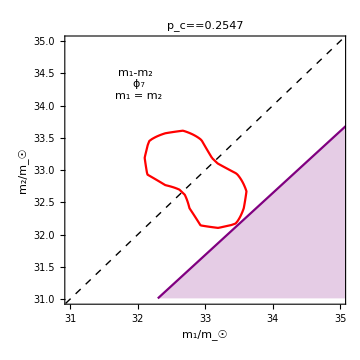

```mathematica
probability=prob;
(*probability=0.2547;*)
(*0.32*)
plots[p]=PlotInversion[p,probability,31,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dphi_3.pdf ...

正在导出矢量图: plot_dphi_2.pdf ...

正在导出矢量图: plot_dphi_4.pdf ...

正在导出矢量图: plot_dphi_5l.pdf ...

正在导出矢量图: plot_dphi_7.pdf ...

正在导出矢量图: plot_dphi_6.pdf ...

```mathematica
Keys[plots]
```

{dphi_3,dphi_2,dphi_4,dphi_5l,dphi_7,dphi_6}

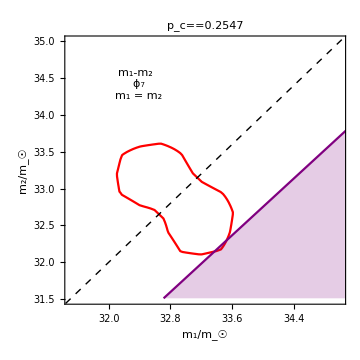
<|dphi_3→-Graphics-,dphi_2→-Graphics-,dphi_4→-Graphics-,dphi_5l→-Graphics-,dphi_7→-Graphics-,dphi_6→-Graphics-|>

```mathematica
plots
```

```mathematica
Keys[plots]
```

{dphi_3,dphi_2,dphi_4,dphi_5l}